# Correlation matrices

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices_CSV","bmv_prices.csv"}];
{{attributes},pricesMatrix} = TakeDrop[Import[path],1];
returnsMatrix = Transpose@Map[Returns,Transpose[pricesMatrix]];
```

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices_CSV","bmv_dates.csv"}];
dates = Import[path];
dates = First@Transpose[dates];
```

```mathematica
pricesPartitioned = Partition[pricesMatrix,152,1];
```

```mathematica
corrMatrices = ProgressTable[Correlation[pricesPartitioned[[i]]],{i,1,Length[pricesPartitioned]}];
```

```mathematica
Manipulate[MatrixPlot[corrMatrices[[i]],PlotLabel->dates[[i]]],{i,1,Length[corrMatrices],1}]
```

```mathematica
GetGraphFromPositiveCorrelations[corrMatrix_,threshold_,attributes_]:=Block[{zeroedCorrMatrices,adjacencyMatrix},
zeroedCorrMatrices = ReplaceAll[corrMatrix,Indeterminate->0];
adjacencyMatrix = ReplaceAll[
zeroedCorrMatrices*(1-IdentityMatrix[Length[zeroedCorrMatrices]]),
{x_ /; (x<threshold)->0,x_ /; (x≥threshold)->1}
];
AdjacencyGraph[adjacencyMatrix,VertexLabels->Thread[Range[Length[attributes]]->attributes]]
];
```

```mathematica
graphs = ProgressTable[GetGraphFromPositiveCorrelations[corrMatrices[[i]],0.7,attributes],{i,1,Length[corrMatrices]}];
```

```mathematica
Manipulate[Labeled[GraphPlot[graphs[[i]],GraphLayout->"CircularEmbedding"],dates[[i]],Top],{i,1,Length[graphs],1}]
```

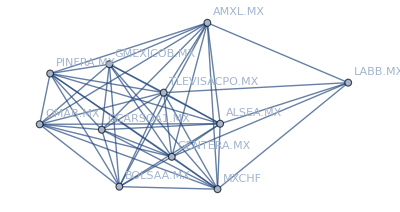

```mathematica
NeighborhoodGraph[graph,4]
```